For the 6-year Rb/Cs clock data in
https://doi-org.iclibezp1.cc.ic.ac.uk/10.1103/PhysRevLett.117.061301

Get the slope of the curve from two points on Fig. 2

```mathematica
logA[ω_]:=Module[{m,b,slope},
slope =Solve[{-16==m(-8.5)+b, -14.5==m(-9)+b},{m,b}][[1]];
If[ω>-8.5,-16,(m*ω+b)/.slope]]
```

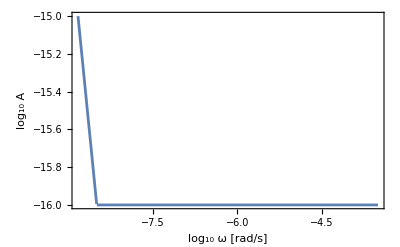

```mathematica
Plot[logA[x],{x,-9, -3.5},Frame->True,PlotRange->{{-9,-3},{-15,-17}},FrameLabel->{"log_10 ω [rad/s]", "log_10 A"}]
```

This is the maximum amplitude of sinusoidal signal in the Rb/Cs frequencies, as a function of the angular frequency of the signal